```mathematica
n=10;
r=5;
magn=1;
numTrials=1000;
SymL5={};
For[i=1,i<numTrials+1,i++,Sym=ResourceFunction["RandomMatrix"]["Symmetric",Real,{-magn,magn},{n,n},"Rank"->r];
Stats=Join[Diagonal[Sym],Flatten[Sym[[1;;5,6;;10]]]];
AppendTo[SymL5,Stats]]
PSDL5={};
For[i=1,i<numTrials+1,i++,PSD=ResourceFunction["RandomMatrix"][Real,{-magn,magn},{n,r}];
PSD=PSD.Transpose[PSD];
Stats=Join[Diagonal[PSD],Flatten[PSD[[1;;5,6;;10]]]];
AppendTo[PSDL5,Stats]]
(*SymPCA=PrincipalComponents[N[SymL5]];
SymPCA//MatrixForm;
PSDPCA=PrincipalComponents[N[PSDL5]];
PSDPCA//MatrixForm;*)
Export["/Users/k87125/Dropbox/Math conferences/Workshop-2020-Warwick/AlgebraicStatistics/ColoredGraphicalModels/SymL5.csv",Transpose[SymL5],"CSV"];
Export["/Users/k87125/Dropbox/Math conferences/Workshop-2020-Warwick/AlgebraicStatistics/ColoredGraphicalModels/PSDL5.csv",Transpose[PSDL5],"CSV"];
```

```mathematica
SymL5//MatrixForm;
```

```mathematica
Histogram[Flatten[SymL5]];
```

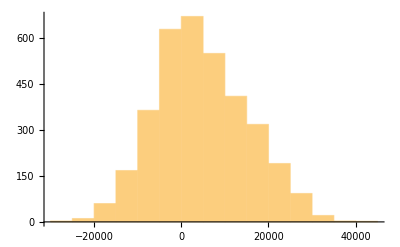

```mathematica
Histogram[Flatten[PSDL5]]
```

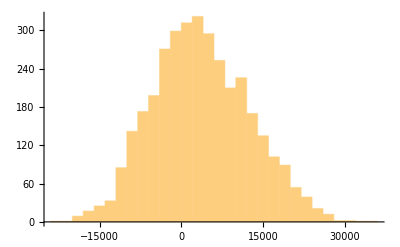

```mathematica
Histogram[Flatten[PSDL4]]
```

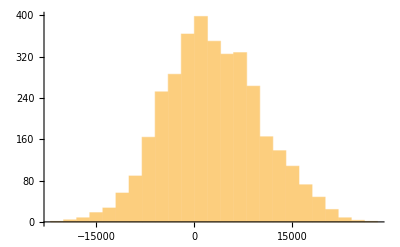

```mathematica
Histogram[Flatten[PSDL3]]
```

```mathematica
PSDL5//MatrixForm
```

(21334. | 28009.8 | 15995.3 | 18588.4 | 5665.71 | 10301.8 | 11015.4 | 10789.9 | 17856.1 | 12911.5 | 4702.97 | -11747.3 | -1045.05 | -1013.63 | -14298.6 | -7185.5 | 11904.4 | 2650.3 | 11785.5 | 22.4128 | 7305.89 | -4505.7 | 345.703 | 1433.16 | -11557. | 796.495 | -5092.5 | 3193.3 | 9864.41 | -686.681 | 4412.23 | -3512.91 | -3402.92 | -3989.77 | -3652.47
34252.9 | 13502. | 8202.2 | 13878.2 | 22935.6 | 18889.8 | 21805.7 | 17793.8 | 18611.4 | 30514.2 | -3885.65 | 3213.65 | -2907.11 | -4843.84 | 1671.38 | -14276.2 | -5598.31 | -10896. | 2573.85 | 3197.52 | -3282.77 | -5056.43 | -2777.47 | 9294.39 | 6195.89 | -9799.76 | -16438.8 | -12802.5 | 9890.08 | -8775.67 | 2117.45 | -3062.49 | 2038.58 | 5979.68 | -17603.2
18487.6 | 12734. | 15112. | 17507.6 | 23146.8 | 27695.6 | 12841. | 7544.4 | 20594.6 | 36481.8 | -20191.5 | 9839.01 | -3785.65 | 5090.68 | -23868.6 | 2368.92 | -46.2767 | -1677.88 | -2215.47 | 5612.57 | 5347.83 | -3865.49 | 6306.85 | -2943.35 | 888.065 | -4972.73 | 1525.96 | 3947.54 | -6040.7 | -9394.7 | -18927. | 5691.19 | -4966.88 | 11732.5 | -17727.
27931.7 | 13610.9 | 12739.7 | 24363.2 | 23706.1 | 16871. | 13560.4 | 18256.7 | 16800.4 | 29983.9 | -2174.11 | 16298.3 | 7817.72 | 5385.71 | 4147.01 | 3102.81 | 6253.85 | 11605.1 | -8843.02 | 5699.9 | -4136.63 | -919.234 | 11249. | -9034.65 | -12320.7 | -3431.54 | 14389.1 | 2644.43 | 10394.2 | 12044.1 | -877.082 | -9656.61 | -20169.1 | 11432.8 | 9856.01
11372.2 | 18772.5 | 19291.3 | 15435.8 | 10742.9 | 13347.3 | 15575.3 | 14236.5 | 22470.3 | 21976.7 | 10528.2 | 6876.83 | -5325.75 | -2798.54 | -5796.86 | -6907.15 | -2083.12 | -2447.9 | -1614.38 | -122.584 | 7715.18 | 4962.08 | -10451.1 | 77.067 | 1601.04 | -9612.5 | -10719.8 | 10141.2 | 1821.86 | -4266.79 | -6526.04 | -9989.58 | -1155.97 | 13023.6 | 304.434
138.655 | 24520.2 | 25140.4 | 12572.9 | 16166.1 | 23388.4 | 16281.2 | 17534.5 | 16573.6 | 21220.7 | 579.676 | 968.816 | 1142.35 | -943.243 | 165.239 | -8876.67 | -14865.8 | -2836.69 | -1990.65 | 18666.7 | 3042.49 | 7280.36 | -10923.3 | 8920.86 | -9862.6 | 1213.75 | -3114.38 | 1795.51 | 3242.43 | -185.661 | 11200.2 | -6148.04 | -4824.18 | 6335.6 | 8611.86
20802.5 | 15198.8 | 12214.1 | 24261.1 | 27548.2 | 13115.3 | 21301.4 | 13003. | 17503.4 | 17530.9 | -4651.03 | -4804.83 | -2478.26 | -7450.92 | -9709.83 | -3815.49 | 3739.4 | 2606.89 | 4226.91 | 5020. | -4564.4 | -3491.5 | 6137.96 | -1275.14 | -8735.58 | 5699.5 | -9972.22 | 2276.13 | 10244.1 | -519.037 | -1557.43 | 1027.76 | -9960.78 | -2083.95 | 821.943
16730.7 | 9304.98 | 23952.5 | 20429.2 | 14652.1 | 12484.7 | 13875. | 26605.8 | 9915.57 | 32970.9 | -9175.17 | 9866.24 | 4764.98 | -7570.13 | -1264.64 | -2998.63 | 8250.46 | 8344.12 | -7056.95 | -8966.21 | -3389.89 | 1204.52 | 24873. | 1149.45 | -1513.59 | 13990.8 | -3550.45 | 1144.6 | 7528.11 | -298.843 | 7573.13 | -7162.45 | 5322.87 | 9941.1 | 7479.55
8546.33 | 18941.1 | 23711.4 | 16740.6 | 23305.1 | 11039.9 | 7994.4 | 11925. | 21626.6 | 6499.2 | -7347.61 | -2454.54 | 5018.34 | 7171.5 | -5033.48 | -1733.14 | 8234.23 | -10300.5 | 10881. | -7747.8 | -8103.64 | -7044.49 | 12672.6 | 9284.94 | -4938.08 | 3478.14 | 9238.78 | -10145.2 | 14368.2 | -7111.84 | 3479.51 | 10879. | -15087.3 | 1265.62 | -288.664
17415.4 | 13385.8 | 10254.6 | 13660.2 | 12134.2 | 12647.2 | 19014. | 26010. | 8157.96 | 20050.3 | 12229.1 | -7388.26 | 15629.4 | 6628.25 | -7348.62 | -5845.6 | 9911.05 | 3326.36 | -5632.85 | 12084.7 | -1532.04 | 8436.59 | 1686.21 | -4474.12 | 3658.11 | 3542.93 | -14875. | -4119.01 | 5426.38 | -11333.5 | 1642.4 | 4717.16 | 4200.61 | 3247.27 | 3540.4)

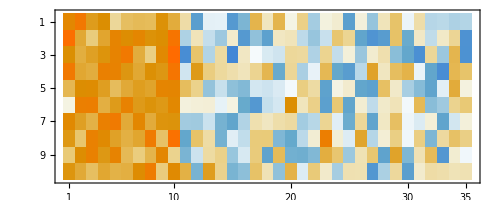

```mathematica
MatrixPlot[%259]
```

```mathematica
n=10;
r=4;
magn=1;
numTrials=2000;
SymL4={};
For[i=1,i<numTrials+1,i++,Sym=ResourceFunction["RandomMatrix"]["Symmetric",Real,{-magn,magn},{n,n},"Rank"->r];
Stats=Join[Diagonal[Sym],Flatten[Sym[[1;;5,6;;10]]]];
AppendTo[SymL4,Stats]]
PSDL4={};
For[i=1,i<numTrials+1,i++,PSD=ResourceFunction["RandomMatrix"][Real,{-magn,magn},{n,r}];
PSD=PSD.Transpose[PSD];
Stats=Join[Diagonal[PSD],Flatten[PSD[[1;;5,6;;10]]]];
AppendTo[PSDL4,Stats]]
(*SymPCA=PrincipalComponents[N[SymL]];
SymPCA//MatrixForm;
PSDPCA=PrincipalComponents[N[PSDL]];
PSDPCA//MatrixForm;*)
Export["/Users/k87125/Dropbox/Math conferences/Workshop-2020-Warwick/AlgebraicStatistics/ColoredGraphicalModels/SymL4.csv",Transpose[SymL4],"CSV"];
Export["/Users/k87125/Dropbox/Math conferences/Workshop-2020-Warwick/AlgebraicStatistics/ColoredGraphicalModels/PSDL4.csv",Transpose[PSDL4],"CSV"];
```

```mathematica
n=10;
r=3;
magn=1;
numTrials=2000;
SymL3={};
For[i=1,i<numTrials+1,i++,Sym=ResourceFunction["RandomMatrix"]["Symmetric",Real,{-magn,magn},{n,n},"Rank"->r];
Stats=Join[Diagonal[Sym],Flatten[Sym[[1;;5,6;;10]]]];
AppendTo[SymL3,Stats]]
PSDL3={};
For[i=1,i<numTrials+1,i++,PSD=ResourceFunction["RandomMatrix"][Real,{-magn,magn},{n,r}];
PSD=PSD.Transpose[PSD];
Stats=Join[Diagonal[PSD],Flatten[PSD[[1;;5,6;;10]]]];
AppendTo[PSDL3,Stats]]
(*SymPCA=PrincipalComponents[N[SymL]];
SymPCA//MatrixForm
PSDPCA=PrincipalComponents[N[PSDL]];
PSDPCA//MatrixForm*)
Export["/Users/k87125/Dropbox/Math conferences/Workshop-2020-Warwick/AlgebraicStatistics/ColoredGraphicalModels/SymL3.csv",Transpose[SymL3],"CSV"];
Export["/Users/k87125/Dropbox/Math conferences/Workshop-2020-Warwick/AlgebraicStatistics/ColoredGraphicalModels/PSDL3.csv",Transpose[PSDL3],"CSV"];
```

```mathematica
SingularValueList[%67]
```

{86421.3,82106.8,79209.3,78992.4,75522.7,72861.4,72635.6,68745.1,66270.1,65122.1,63937.6,62664.9,58572.8,57738.7,57255.5,55525.8,51575.7,50660.9,49259.5,48239.8,45944.4,44906.8,42444.1,41585.7,41071.1,40199.8,37489.4,35627.1,33922.1,33152.8,31586.3,30818.8,28263.1,25575.4,24267.7}

```mathematica
Dimensions[%67]
```

{100,35}

```mathematica
SeedRandom[314];data=RandomReal[{0,1},{10,3}];
ph=ResourceFunction["PersistentHomology"][data]
```

PersistentHomologyObject[…]

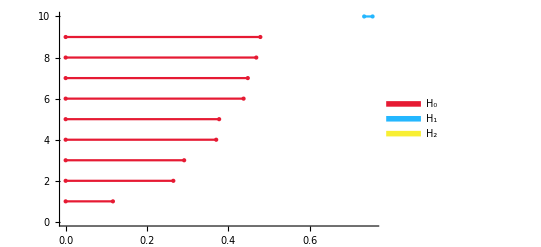

```mathematica
PersistentHomologyObject[…]
ph["Barcode"]
```

```mathematica
ph5=ResourceFunction["PersistentHomology"][PSDL5];
```

Subsets::toomany: The number of subsets (4206774902900425037748196880) indicated by Subsets[{1,2,3,4,5,6,7,8,9,10,«90»},36] is too large; it must be a machine integer.

Set::shape: Lists {FunctionRepository`$645ddbd3626848df9e4b4c4a2d6dd9d0`sortedsimps$25761,FunctionRepository`$645ddbd3626848df9e4b4c4a2d6dd9d0`sortweights$25761} and {} are not the same shape.

PositionIndex::invrp: The argument FunctionRepository`$645ddbd3626848df9e4b4c4a2d6dd9d0`sortedsimps$25761 is not a valid Association or a list.

Part::partd: Part specification PositionIndex[FunctionRepository`$645ddbd3626848df9e4b4c4a2d6dd9d0`sortedsimps$25761]⟦All,1⟧ is longer than depth of object.

Subsets::toomany: The number of subsets (1977204582144932989443770175) indicated by Subsets[{1,2,3,4,5,6,7,8,9,10,«90»},{36}] is too large; it must be a machine integer.

Catenate::invrp: The argument Subsets[{1,2,3,4,5,6,7,8,9,10,«90»},{36}] is not a valid Association or a list.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
ph5["Barcode"]
```

-Graphics-

```mathematica
ph5["GeneratorMeshes"]
```

{}

```mathematica
PSDL5[[1]]
```

{3.09624,1.11591,3.02825,2.01597,1.21886,1.02106,2.78015,2.44882,1.26423,1.40011,-0.272045,0.553629,-1.49993,-0.271816,-1.18544,-0.146082,-1.09292,-0.653183,-0.0471308,0.730753,0.768643,-1.59534,0.485471,0.982019,0.711315,0.451108,-0.721937,1.30522,-0.91271,0.0537231,-0.257271,1.6795,-0.152633,0.193241,-0.674191}

```mathematica
ph4=ResourceFunction["PersistentHomology"][PSDL4];
```

Subsets::toomany: The number of subsets (4206774902900425037748196880) indicated by Subsets[{1,2,3,4,5,6,7,8,9,10,«90»},36] is too large; it must be a machine integer.

Set::shape: Lists {FunctionRepository`$645ddbd3626848df9e4b4c4a2d6dd9d0`sortedsimps$27024,FunctionRepository`$645ddbd3626848df9e4b4c4a2d6dd9d0`sortweights$27024} and {} are not the same shape.

PositionIndex::invrp: The argument FunctionRepository`$645ddbd3626848df9e4b4c4a2d6dd9d0`sortedsimps$27024 is not a valid Association or a list.

Part::partd: Part specification PositionIndex[FunctionRepository`$645ddbd3626848df9e4b4c4a2d6dd9d0`sortedsimps$27024]⟦All,1⟧ is longer than depth of object.

Subsets::toomany: The number of subsets (1977204582144932989443770175) indicated by Subsets[{1,2,3,4,5,6,7,8,9,10,«90»},{36}] is too large; it must be a machine integer.

Catenate::invrp: The argument Subsets[{1,2,3,4,5,6,7,8,9,10,«90»},{36}] is not a valid Association or a list.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
ph4["Barcode"]
```

-Graphics-

```mathematica
myMatrix[n_Integer,m_Integer]:=Table[Subscript[x,i,j],{i,n},{j,m}]
M=myMatrix[10,10];
```

{{x_(1,1),x_(1,2),x_(1,3),x_(1,4),x_(1,5),x_(1,6),x_(1,7),x_(1,8),x_(1,9),x_(1,10)},{x_(2,1),x_(2,2),x_(2,3),x_(2,4),x_(2,5),x_(2,6),x_(2,7),x_(2,8),x_(2,9),x_(2,10)},{x_(3,1),x_(3,2),x_(3,3),x_(3,4),x_(3,5),x_(3,6),x_(3,7),x_(3,8),x_(3,9),x_(3,10)},{x_(4,1),x_(4,2),x_(4,3),x_(4,4),x_(4,5),x_(4,6),x_(4,7),x_(4,8),x_(4,9),x_(4,10)},{x_(5,1),x_(5,2),x_(5,3),x_(5,4),x_(5,5),x_(5,6),x_(5,7),x_(5,8),x_(5,9),x_(5,10)},{x_(6,1),x_(6,2),x_(6,3),x_(6,4),x_(6,5),x_(6,6),x_(6,7),x_(6,8),x_(6,9),x_(6,10)},{x_(7,1),x_(7,2),x_(7,3),x_(7,4),x_(7,5),x_(7,6),x_(7,7),x_(7,8),x_(7,9),x_(7,10)},{x_(8,1),x_(8,2),x_(8,3),x_(8,4),x_(8,5),x_(8,6),x_(8,7),x_(8,8),x_(8,9),x_(8,10)},{x_(9,1),x_(9,2),x_(9,3),x_(9,4),x_(9,5),x_(9,6),x_(9,7),x_(9,8),x_(9,9),x_(9,10)},{x_(10,1),x_(10,2),x_(10,3),x_(10,4),x_(10,5),x_(10,6),x_(10,7),x_(10,8),x_(10,9),x_(10,10)}}

```mathematica
PSD=ResourceFunction["RandomMatrix"][Real,{-1,1},{10,4}];
PSD=PSD.Transpose[PSD];
```

```mathematica
For[i =1,i<11,i++,Subscript[x,i,i]=PSD[[i,i]]]
For[i =1,i<6,i++,
For[j=6,j<11,j++,Subscript[x,i,j]=PSD[[i,j]]]]
```

```mathematica
Length[Variables[M]]
```

65

```mathematica
Coef=RandomInteger[{-100,100},{Length[Variables[M]],1}];
```

```mathematica
opt=SemidefiniteOptimization[(Variables[M].Coef)[[1,1]],M(\[VectorGreaterEqual])_Length[M] 0,Variables[M]]
```

SemidefiniteOptimization::herm: The matrix … is not Hermitian or real and symmetric.

SemidefiniteOptimization[-9 x_(1,2),{{0.416267,x_(1,2),x_(1,3),x_(1,4),x_(1,5),-0.359643,0.301409,0.593011,0.00910709,-0.652936},{x_(2,1),0.684383,x_(2,3),x_(2,4),x_(2,5),0.106037,-0.0663786,0.652522,0.074501,-0.346655},{x_(3,1),x_(3,2),1.86454,x_(3,4),x_(3,5),0.014245,-0.194154,-0.31377,0.271694,0.295737},{x_(4,1),x_(4,2),x_(4,3),1.12368,x_(4,5),0.145346,0.0575021,-0.377545,-0.299463,0.267373},{x_(5,1),x_(5,2),x_(5,3),x_(5,4),1.20795,0.0113434,-0.412869,0.522731,0.0740479,-0.102955},{x_(6,1),x_(6,2),x_(6,3),x_(6,4),x_(6,5),0.748329,x_(6,7),x_(6,8),x_(6,9),x_(6,10)},{x_(7,1),x_(7,2),x_(7,3),x_(7,4),x_(7,5),x_(7,6),0.639746,x_(7,8),x_(7,9),x_(7,10)},{x_(8,1),x_(8,2),x_(8,3),x_(8,4),x_(8,5),x_(8,6),x_(8,7),1.40794,x_(8,9),x_(8,10)},{x_(9,1),x_(9,2),x_(9,3),x_(9,4),x_(9,5),x_(9,6),x_(9,7),x_(9,8),0.153583,x_(9,10)},{x_(10,1),x_(10,2),x_(10,3),x_(10,4),x_(10,5),x_(10,6),x_(10,7),x_(10,8),x_(10,9),1.27883}}(\[VectorGreaterEqual])_10 0,{x_(1,2),x_(1,3),x_(1,4),x_(1,5),x_(2,1),x_(2,3),x_(2,4),x_(2,5),x_(3,1),x_(3,2),x_(3,4),x_(3,5),x_(4,1),x_(4,2),x_(4,3),x_(4,5),x_(5,1),x_(5,2),x_(5,3),x_(5,4),x_(6,1),x_(6,2),x_(6,3),x_(6,4),x_(6,5),x_(6,7),x_(6,8),x_(6,9),x_(6,10),x_(7,1),x_(7,2),x_(7,3),x_(7,4),x_(7,5),x_(7,6),x_(7,8),x_(7,9),x_(7,10),x_(8,1),x_(8,2),x_(8,3),x_(8,4),x_(8,5),x_(8,6),x_(8,7),x_(8,9),x_(8,10),x_(9,1),x_(9,2),x_(9,3),x_(9,4),x_(9,5),x_(9,6),x_(9,7),x_(9,8),x_(9,10),x_(10,1),x_(10,2),x_(10,3),x_(10,4),x_(10,5),x_(10,6),x_(10,7),x_(10,8),x_(10,9)}]